```mathematica
pdfToCDF[pdf_]:=
Module[{x,y},
x=Join[{pdf[[1,1]]},Most[pdf[[All,1]]]+Differences[pdf[[All,1]]]/2,{pdf[[-1,1]]}];
y=Prepend[#/Last[#]&@Accumulate[pdf[[All,2]]*Differences[x]],0.];
Transpose@{x,y}
]
```

```mathematica
jitterList[l_,tol_]:=Catenate[#+tol*Range[0,Length[#]-1]&/@Split[l]]
jitterPoints[pts_,tol_:$MachineEpsilon*10]:=SubsetMap[jitterList[#,tol]&,SubsetMap[jitterList[#,tol]&,pts,{All,1}],{All,2}]
```

```mathematica
truncatePDF[pdf_,rawInterval_Interval]:=
With[
{interval=IntervalIntersection[rawInterval,Interval[MinMax[pdf[[All,1]]]]]},
{filteredPDF=Pick[pdf,IntervalMemberQ[interval,pdf[[All,1]]],False]},
{if=Interpolation[jitterPoints@pdf,InterpolationOrder->1,Method->"Hermite"]},
SortBy[
Join[
filteredPDF,
Catenate[{{#[[1]],if[#[[1]]]},{#[[1]]+10*$MachineEpsilon,0},{#[[2]]-10*$MachineEpsilon,0},{#[[2]],if[#[[2]]]}}&/@List@@interval]
],
First
]
]
```

```mathematica
griddyGibbsSample[pdf_,n_]:=
With[
{cdf=pdfToCDF[pdf]},
{if=Interpolation[jitterPoints[Reverse/@cdf],Method->"Hermite",InterpolationOrder->1]},
if[RandomReal[{0,1},n]]
]
griddyGibbsSample[pdf_]:=griddyGibbsSample[pdf,1]
```

```mathematica
pdf=Transpose[{N@{1,2,5,6},{0.4,1.,0.6,0.3}}]
```

{{1.,0.4},{2.,1.},{5.,0.6},{6.,0.3}}

InterpolatingFunction::dmval: Input value {-0.112662} lies outside the range of data in the interpolating function. Extrapolation will be used.

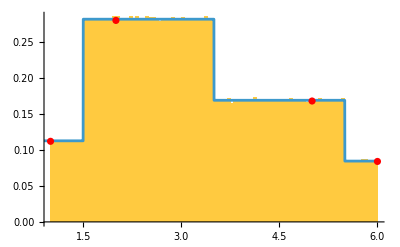

```mathematica
Show[{
Histogram[griddyGibbsSample[pdf,1000000],100,"PDF"],
Plot[Evaluate[D[InverseFunction[Interpolation[jitterPoints[Reverse/@pdfToCDF[pdf]],Method->"Hermite",InterpolationOrder->1]][x],x]],{x,0,6}],
ListPlot[SubsetMap[#*0.28&,pdf,{All,2}],PlotStyle->Red]
}]
```

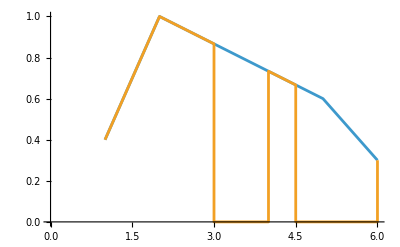

```mathematica
ListLinePlot[{pdf,truncatePDF[pdf,Interval[{3,4},{4.5,6}]]}]
```

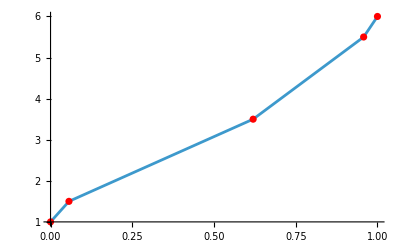

```mathematica
With[{if=Interpolation[Reverse/@jitterPoints@pdfToCDF[pdf],InterpolationOrder->1]},
Show[{
Plot[if[x],{x,0,1}],
ListPlot[Reverse/@pdfToCDF[pdf],PlotStyle->Red]
}]
]
```

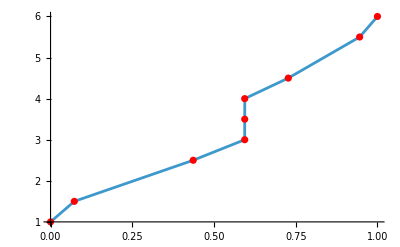

```mathematica
With[{if=Interpolation[Reverse/@jitterPoints@pdfToCDF[truncatePDF[pdf,Interval[{3,4}]]],InterpolationOrder->1]},
Show[{
Plot[if[x],{x,0,1}],
ListPlot[Reverse/@pdfToCDF[truncatePDF[pdf,Interval[{3,4}]]],PlotStyle->Red]
}]
]
```

### Log space version

```mathematica
cLogCDF:=cLogCDF=FunctionCompile[FunctionDeclaration[logSumExpPlus,Function[{Typed[a,"MachineReal"],Typed[b,"MachineReal"]},With[{c=Max[a,b]},c+Log[Exp[a-c]+Exp[b-c]]]]],Function[Typed[logPDF,"PackedArray"::["MachineReal",1]],With[{cdf=FoldList[logSumExpPlus,logPDF]},cdf-Last[cdf]]]];

logPDFToLogCDF[logPDF_]:=Module[{x,y},x=Join[{logPDF[[1,1]]},Most[logPDF[[All,1]]]+Differences[logPDF[[All,1]]]/2,{logPDF[[-1,1]]}];
y=Prepend[cLogCDF[logPDF[[All,2]]+Log[Differences[x]]],-$MaxMachineNumber];
Transpose@{x,y}]
```

```mathematica
griddyGibbsSampleLog[logPDF_,n_]:=With[{logCDF=logPDFToLogCDF[logPDF]},{if=Interpolation[jitterPoints[Reverse/@logCDF],Method->"Hermite",InterpolationOrder->1]},if[Log@RandomReal[{0,1},n]]]
griddyGibbsSampleLog[pdf_]:=griddyGibbsSampleLog[pdf,1]
```

```mathematica
logPDF=Transpose[{N@{1,2,5,6},Log@{0.4,1.,0.6,0.3}}]
```

{{1.,-0.916291},{2.,0.},{5.,-0.510826},{6.,-1.20397}}

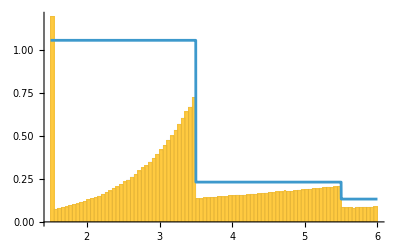

```mathematica
Show[{
Histogram[griddyGibbsSampleLog[logPDF,1000000],100,"PDF"],
Plot[Evaluate[D[InverseFunction[Interpolation[jitterPoints[Reverse/@logPDFToLogCDF[pdf]],Method->"Hermite",InterpolationOrder->1]][x],x]],{x,0,6}]
}]
```

## OLD

```mathematica
x=Range[-10,10,0.1];
```

```mathematica
w=Normalize[PDF[NormalDistribution[0.3,3.2],x],Total];
```

```mathematica
w2=Normalize[PDF[NormalDistribution[0.6,3.2],x],Total];
```

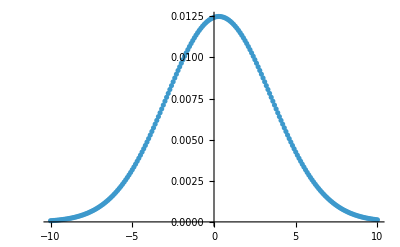

```mathematica
ListPlot@Transpose@{x,w}
```

```mathematica
Interpolation[Transpose[{x,Transpose[{w,w2}]}]][5]//RepeatedTiming
```

{0.000199602,{0.00424709,0.00485389}}

```mathematica
Interpolation[Transpose[{x,Transpose[ConstantArray[w,100]]}]][Range[-10,10,0.01]];//RepeatedTiming
```

{0.0772268,Null}

```mathematica
Interpolation[Transpose[{x,w}]][Range[-10,10,0.01]];//RepeatedTiming
```

{0.00172367,Null}

```mathematica
With[{if=Interpolation[Transpose[{x,Transpose[{w,w2}]}]]},if[Range[-10,10,0.01]];//RepeatedTiming]
```

{0.00011574,Null}

```mathematica
Total@w
```

1.

```mathematica
if=Interpolation[Prepend[Transpose@{Accumulate@w,x},{0,0}],InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
Around@if[RandomReal[{0,1},10000]]
```

0.23.2

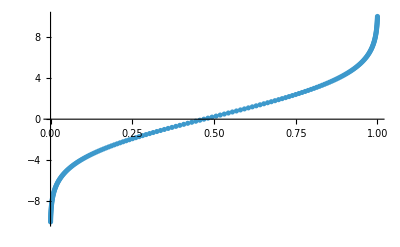

```mathematica
ListPlot[Transpose@{Accumulate@w,x},PlotRange->All]
```

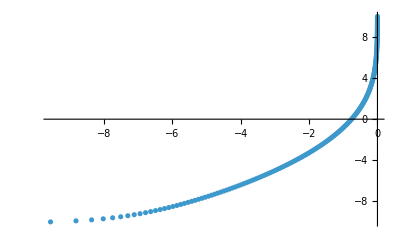

```mathematica
ListPlot[Transpose@{Log@Accumulate@w,x},PlotRange->All]
```

```mathematica
InverseFunction[Function[x,CDF[ExponentialDistribution[λ],x]]][y]
```

InverseFunction[Function[x,CDF[ExponentialDistribution[λ],x]]][y]

```mathematica
CDF[ExponentialDistribution[λ],x]
```

Piecewise[{{1-ⅇ^(-x λ), x≥0}, {0, True}}]

```mathematica
FullSimplify@Solve[CDF[NormalDistribution[μ,σ],x]==y,x,Reals]
```

{{x→ConditionalExpression[μ-√2 σ InverseErfc[2 y], 0<y<1]}}

```mathematica
FullSimplify@Solve[CDF[ExponentialDistribution[λ],x][[1,1,1]]==y,x,Reals]
```

{{x→ConditionalExpression[-Log[1-y]/λ, y<1]}}

```mathematica
Assuming[x>=0,CDF[ExponentialDistribution[λ],x]]
```

Piecewise[{{1-ⅇ^(-x λ), x≥0}, {0, True}}]

```mathematica
CDF[ExponentialDistribution[λ],x][[1,1,1]]
```

1-ⅇ^(-x λ)

```mathematica
logSumExp[m_,level_:0]:=With[{c=Map[Max,m,{level}]},c+Log[Total[Exp[m-c],{level+1}]]]
```

```mathematica
logSumExp[{a,b}]
```

Log[ⅇ^(a-Max[a,b])+ⅇ^(b-Max[a,b])]+Max[a,b]

```mathematica
logSumExpPlus[a_,b_]:=With[{c=Max[a,b]},c+Log[Exp[a-c]+Exp[b-c]]]
```

```mathematica
Exp[logSumExp[{Log[3],Log[2]}]]
```

5

```mathematica
Exp[logSumExpPlus[Log[3],Log[2]]]
```

5

```mathematica
logCDF[logPDF_]:=With[{cdf=FoldList[logSumExpPlus,logPDF]},cdf-Last[cdf]]
```

```mathematica
pdf=Log@PDF[NormalDistribution[1.3,0.6],Range[-5,5,0.01]];
```

```mathematica
logCDF[pdf];//RepeatedTiming
```

{0.00201394,Null}

```mathematica
cLogCDF[pdf];//RepeatedTiming
```

{0.0000291474,Null}

```mathematica
cLogCDF[pdf]==logCDF[pdf]
```

True

```mathematica
cLogCDF=FunctionCompile[
FunctionDeclaration[logSumExpPlus,
Function[{Typed[a,"MachineReal"],Typed[b,"MachineReal"]},
With[{c=Max[a,b]},c+Log[Exp[a-c]+Exp[b-c]]]
]
],
Function[Typed[logPDF,"PackedArray"::["MachineReal",1]],
With[{cdf=FoldList[logSumExpPlus,logPDF]},cdf-Last[cdf]]
]
]
```

CompiledCodeFunction[…]

```mathematica
cLogCDF=FunctionCompile[
FunctionDeclaration[logSumExpPlus,Typed[{"MachineReal","MachineReal"}->"MachineReal"]@DownValuesFunction[logSumExpPlus]],
Typed[{"PackedArray"::["MachineReal",1]}->"PackedArray"::["MachineReal",1]]@DownValuesFunction[logCDF]
]
```

CompiledCodeFunction[…]

```mathematica
Log@PDF[NormalDistribution[0.,1.],-1000.]
```

-500000.918938533

```mathematica
logCDF=cLogCDF;
```

```mathematica
(*logPDFToCDF[logPDF_]:=With[{cdf=Accumulate@Exp[logPDF]},cdf/Last[cdf]]*)
```

```mathematica
pdfToCDF[samplePoints_,pdf_]:=
Module[{x,y},
x=Join[{samplePoints[[1]]},Most[samplePoints]+Differences[samplePoints]/2,{samplePoints[[-1]]}];
y=Prepend[#/Last[#]&@Accumulate[pdf*Differences[x]],0.];
Transpose@{x,y}
]
```

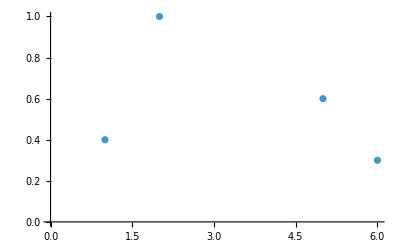

```mathematica
ListPlot[Transpose@{N@{1,2,5,6},{0.4,1.,0.6,0.3}}]
```

```mathematica
1/2*0.4
```

0.2

```mathematica
pdfToCDF[N@{1,2,5,6},{0.4,1.,0.6,0.3}]
```

{{1.,0.},{1.5,0.056338},{3.5,0.619718},{5.5,0.957746},{6.,1.}}

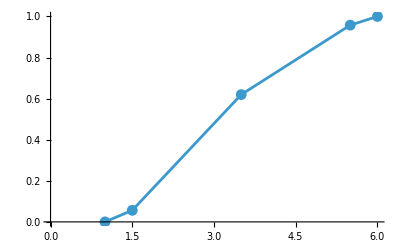

```mathematica
ListLinePlot[pdfToCDF[N@{1,2,5,6},{0.4,1.,0.6,0.3}],Mesh->All]
```

```mathematica
if=Interpolation[pdfToCDF[N@{1,2,5,6},{0.4,1.,0.6,0.3}],InterpolationOrder->1]
```

InterpolatingFunction[…]

InterpolatingFunction::dmval: Input value {0.000122571} lies outside the range of data in the interpolating function. Extrapolation will be used.

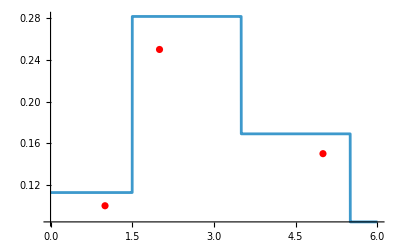

```mathematica
Show[{
Plot[if'[x],{x,0,6}],
ListPlot[Transpose@{N@{1,2,5,6},{0.4,1.,0.6,0.3}*0.25},PlotStyle->Red]
}]
```

InterpolatingFunction::dmval: Input value {0.000122571} lies outside the range of data in the interpolating function. Extrapolation will be used.

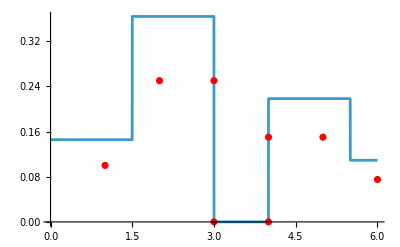

```mathematica
With[{if=Interpolation[pdfToCDF[N@{1,2,3,3+$MachineEpsilon,4,4+$MachineEpsilon,5,6},{0.4,1.,1.,0,0,0.6,0.6,0.3}],InterpolationOrder->1]},
Show[{
Plot[if'[x],{x,0,6}],
ListPlot[Transpose@{N@{1,2,3,3+$MachineEpsilon,4,4+$MachineEpsilon,5,6},{0.4,1.,1.,0,0,0.6,0.6,0.3}*0.25},PlotStyle->Red]
}]
]
```

```mathematica
jitterList[l_,tol_]:=Catenate[#+tol*Range[0,Length[#]-1]&/@Split[l]]
jitterPoints[pts_,tol_:$MachineEpsilon*10]:=SubsetMap[jitterList[#,tol]&,SubsetMap[jitterList[#,tol]&,pts,{All,1}],{All,2}]
```

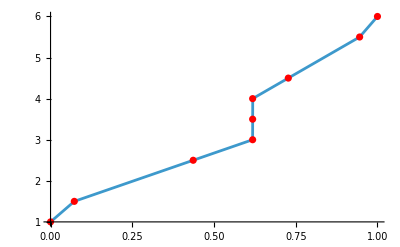

```mathematica
With[{if=Interpolation[DeleteAdjacentDuplicates[Reverse/@jitterPoints@pdfToCDF[N@{1,2,3,3,4,4,5,6},{0.4,1.,1.,0,0,0.6,0.6,0.3}],#2[[1]]-#1[[1]]<$MachineEpsilon&],InterpolationOrder->1]},
Show[{
Plot[if[x],{x,0,1}],
ListPlot[Reverse/@jitterPoints@pdfToCDF[N@{1,2,3,3,4,4,5,6},{0.4,1.,1.,0,0,0.6,0.6,0.3}],PlotStyle->Red]
}]
]
```

```mathematica
if=Interpolation[Transpose@pdfToCDF[N@{1,2,5,6},{0.4,1.,0.6,0.3}],InterpolationOrder->1]
```

InterpolatingFunction[…]

InterpolatingFunction::dmval: Input value {0.000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

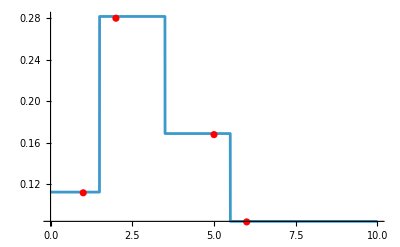

```mathematica
Show[{
Plot[if'[x],{x,0,10},PlotRange->All],
ListPlot[Transpose@{{1,2,5,6},{0.4,1.,0.6,0.3}*.28},PlotStyle->Red]
}]
```

```mathematica
griddyGibbsSample[logPMF_,samplePoints_]:=
With[
{w=logPMF[samplePoints]},
{wTotal=logCDF[w]},
{if=Interpolation[
GatherBy[Transpose[{wTotal,samplePoints}],First][[All,1]],
Method->"Hermite",InterpolationOrder->1
]},
if[Log@RandomReal[{0,1}]]
]
```

```mathematica
griddyGibbsSample[logPMF_,samplePoints_]:=
With[
{cdf=pdfToCDF[samplePoints,Exp@logPMF[samplePoints]]},
{if=Interpolation[
DeleteAdjacentDuplicates[Reverse/@cdf,#1[[1]]==#2[[1]]&],
Method->"Hermite",InterpolationOrder->1
]},
if[RandomReal[{0,1}]]
]
```

```mathematica
Mean@Table[griddyGibbsSample[Map[LogLikelihood[NormalDistribution[1.3,0.4],{#}]&],Range[-3,3,0.1]+RandomReal[{-0.5,0.5}]],10000]
```

1.29552

```mathematica
Mean@Table[griddyGibbsSample[Map[LogLikelihood[NormalDistribution[1.3,0.4],{#}]&],Range[-3,3,1.]+RandomReal[{-0.5,0.5}]],10000]
```

1.29863

```mathematica
Mean@Table[griddyGibbsSample[Map[LogLikelihood[NormalDistribution[1.3,0.4],{#}]&],Range[-3.5,2.5,1.]+RandomReal[{-0.5,0.5}]],10000]
```

1.2776

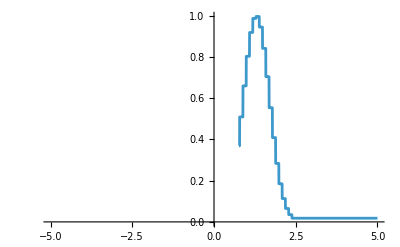

```mathematica
Plot[Evaluate[D[InverseFunction[InterpolatingFunction[…]][x],x]],{x,-5,5}]
```

```mathematica
griddyGibbsSample[Map[LogLikelihood[NormalDistribution[1.3,0.6],{#}]&],Range[-10,10,0.3]+RandomReal[{0,1}]]
```

InterpolatingFunction[…]

1.50231

```mathematica
griddyGibbsSample[Map[LogLikelihood[NormalDistribution[1.3,0.6],{#}]&],Range[-10,10,1.]+RandomReal[{0,1}]]//RepeatedTiming
```

{0.000270515,-0.397088}

```mathematica
Histogram@Table[griddyGibbsSample[Map[LogLikelihood[NormalDistribution[1.3,0.4],{#}]&],Range[-10,10,1]+RandomReal[{-0.5,0.5}]],1000]//EchoTiming
```

0.28791

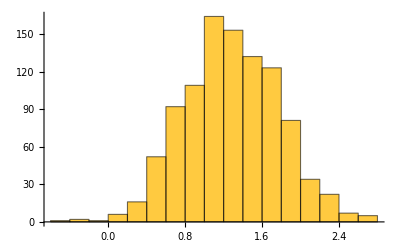

```mathematica
Around@Table[griddyGibbsSample[Map[LogLikelihood[NormalDistribution[1.3,0.4],{#}]&],Range[-3,3,0.1]+RandomReal[{-0.5,0.5}]],10000]
```

1.30.4

```mathematica
Around@Table[griddyGibbsSample[Map[LogLikelihood[NormalDistribution[1.3,0.4],{#}]&],Range[-3,3,1]+RandomReal[{-0.5,0.5}]],10000]
```

1.30.5

```mathematica
Histogram@Table[griddyGibbsSample[Map[LogLikelihood[NormalDistribution[1.3,0.4],{#}]&],Range[-3,3,1.]+RandomReal[{-0.5,0.5}]],10000]//EchoTiming
```

```mathematica
Histogram@Table[griddyGibbsSample[Map[LogLikelihood[NormalDistribution[1.3,0.4],{#}]&],Range[-3,3,0.1]+RandomReal[{-0.5,0.5}]],10000]//EchoTiming
```

7.80037

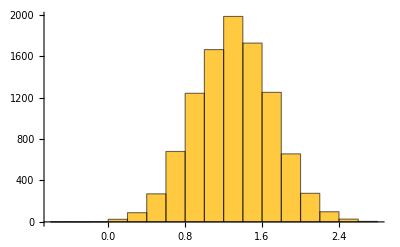

```mathematica
Interpolation[Log@{{0,0},{1,1},{2,3}},InterpolationOrder->1]
```

Interpolation::indat: Data point {-∞,-∞} contains abscissa -∞, which is not a real number.

Interpolation[{{-∞,-∞},{0,0},{Log[2],Log[3]}},InterpolationOrder→1]

```mathematica
PDF[NormalDistribution[1.3,0.6]]
```

Function[x,0.664904 ⅇ^(-1.38889 (-1.3+x)^2)]

```mathematica
x=Range[-10,10,1.];
```

```mathematica
y=Log@PDF[NormalDistribution[1.3,0.6],x]
```

{-177.755,-147.755,-120.533,-96.0887,-74.422,-55.5331,-39.422,-26.0887,-15.5331,-7.75534,-2.75534,-0.533113,-1.08867,-4.422,-10.5331,-19.422,-31.0887,-45.5331,-62.7553,-82.7553,-105.533}

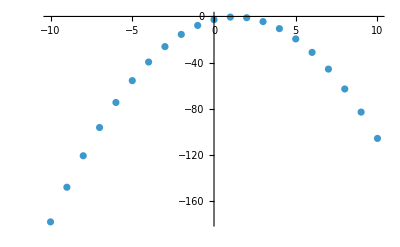

```mathematica
ListPlot[Transpose[{x,y}]]
```